```mathematica
(*local="/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/model_driven_theory/2019"
SetDirectory[local]
incr1={(*1,3,6,*)9}
dayst={1,3,7,14(*6,9,12,14,18*)}
dayst={1,2,3,4(*6,9,12,14,18*)}
sigma=0.06 (*0.01,0.03,0.06*)
rg=dayst(*,10}*);
rg=Range[0,25];
filename=Flatten[Table[
{(*"cellcycletheory-sc-"<>ToString[#]<>"-rp1--5-52.-11111-1-5-5-5-0-1-"<>ToString[incr]*)
(*"cellcycletheory-sc-"<>ToString[#]<>"-rp1--5-42.-1111-1-5-5-5-0-1-"<>ToString[incr]*)
"cellcycletheory-sc-"<>ToString[#]<>"-rp1-"<>ToString[sigma]<>"-52.-11111-"<>If[incr<0,"2","0.5"]<>"-5-5-5-0-1-"<>ToString[incr]
}&/@rg,
{incr,incr1}]]
ccd1=ReadList[local<>"/data3D/"<>#<>"-0-0-0-0.5-5-2-2-1-2--1--2-0.01-0.01-0.3--1-0.dat"]&/@filename;
ccd=ccd1[[All,All,4]];*)
```

```mathematica
(*diversity2={Mean[#[[All,4]]],Length[Union[#[[All,8;;All]]]]}&/@ccd1*)
```

```mathematica
ccdList={-2,1,1.25,1.5,1.75,2.5,6}
ccdList={-2,1,1.25,1.5,1.75,2.5,6}
cL[x_,ccdList_]:=Flatten[If[(#[[1]]≤x)&&(x<#[[2]]),Position[Partition[ccdList,2,1],#],{}]&/@Partition[ccdList,2,1]]
cL[#,ccdList]&/@ccdList

coloB=Table[Blend[{ColorData["ThermometerColors"][0.15],Lighter[Pink,0.75]},i],{i,0,1.15,0.2}]
col[x_]:=Reverse[coloB][[x]]
```

{-2,1,1.25,1.5,1.75,2.5,6}

{-2,1,1.25,1.5,1.75,2.5,6}

{{1},{2},{3},{4},{5},{6},{}}

{RGBColor[0.3536047, 0.46289399999999997, 0.9223703],RGBColor[0.48288376, 0.5453152, 0.91289624],RGBColor[0.61216282, 0.6277364, 0.90342218],RGBColor[0.74144188, 0.7101576, 0.89394812],RGBColor[0.87072094, 0.7925788, 0.88447406],RGBColor[1., 0.875, 0.875]}

```mathematica
(*pos=.
bc=fc=dc=Tuples[{{}},Length[ccd]-1][[1]]
Table[
fc[[i]]=SplitBy[(Sort[{cL[#,ccdList][[1]],#}&/@ccd[[i]]]/."NA"->0),First];
,{i,1,Length[ccd]}];
fc
Table[bc[[i]]={0,0,0,0,0,0};((bc[[i]][[Mean[#[[All,1]]]]]=Length[#])&/@fc[[i]]);
(*bc[[i]]=N[bc[[i]]/Total[bc[[i]]]];*),{i,1,Length[fc]}];*)
```

```mathematica
diversity2={{0.5,1},{0.5611456409692364,1},{0.6218427691696853,1},{0.6524226605091884,1},{0.6788840178446524,1},{0.696521145097867,1},{0.7233156708878556,2},{0.742922226628043,2},{0.7514487449321886,2},{0.7585500608716526,2},{0.7710173710109393,2},{0.7812865325113197,2},{0.7935900269179319,2},{0.8041753326654754,2},{0.8181229127251638,2},{0.8303477810570108,2},{0.8320890325514757,4},{0.8338112058337974,3},{0.8382691569316031,3},{0.8423935156854216,3},{0.8476323004170107,3},{0.8522788660871489,3},{0.8586035651585627,3},{0.8643634692542255,3},{0.8693981184755816,3},{0.8740698804742891,3},{0.5,1},{0.6797770288790699,1},{0.860047987126277,1},{0.9507058191176846,1},{1.040830506215046,2},{1.1005889412489727,2},{1.1698913327717113,4},{1.2215128783601783,4},{1.2612559176147,4},{1.2925376464406113,4},{1.331422514794277,8},{1.363952753229587,8},{1.397127665717419,8},{1.4255757590618099,8},{1.4600080577844186,15},{1.4902706422464171,15},{1.5060657227951424,15},{1.5198828449389534,15},{1.5390030975563889,15},{1.5561735744869105,15},{1.5739764315673126,15},{1.5901928489292905,15},{1.608686547113508,18},{1.6258917293168849,17},{1.6419360422694185,17},{1.6567551144095394,17},{0.5,1},{0.8599214737584333,1},{1.2199808101192735,2},{1.3999550548977227,2},{1.5799119152770824,6},{1.6997140862471283,5},{1.8362040085648423,16},{1.9386611063360495,16},{2.0183811456552756,16},{2.082383283838759,16},{2.166183396879778,48},{2.235779265932171,48},{2.2973703029116668,48},{2.3501374375683777,48},{2.418366022631306,72},{2.477991885969258,72},{2.5097650367220967,72},{2.537996160561081,72},{2.5811959026770133,72},{2.6199521942018724,72},{2.6552538302822937,72},{2.687327573744098,72},{2.724214471542535,74},{2.7579312940831,73},{2.790901877461926,82},{2.8212346694037054,82},
{0.5,1},{1.0394583123709624,1},{1.5791110012049394,2},{1.8487191105142007,2},{2.118574231652217,16},{2.2985310854961893,16},{2.504429938579242,48},{2.6591687035601015,48},{2.779332843578328,48},{2.875197882882623,48},{3.0025132440765843,76},{3.1086687113654996,76},{3.1992026372397038,83},{3.2766562469630793,83},{3.3796023258005516,164},{3.4696666204931437,164},{3.5172788692934196,164},{3.559516130360532,164},{3.625380334596688,176},{3.684765282630737,176},{3.737901903455028,180},{3.7861525231718938,180},{3.841167320836345,280},{3.891417026659062,280},{3.9408420173991945,338},{3.9863983591757277,338}};
(*diversity=Flatten[(Transpose[#]&/@Partition[diversity2,26]),1][[{2,4,6,8}]]*)
diversity1=Flatten[(Transpose[#]&/@Partition[diversity2,26]),1][[{1,3,5,7}]]
```

{{0.5,0.561146,0.621843,0.652423,0.678884,0.696521,0.723316,0.742922,0.751449,0.75855,0.771017,0.781287,0.79359,0.804175,0.818123,0.830348,0.832089,0.833811,0.838269,0.842394,0.847632,0.852279,0.858604,0.864363,0.869398,0.87407},{0.5,0.679777,0.860048,0.950706,1.04083,1.10059,1.16989,1.22151,1.26126,1.29254,1.33142,1.36395,1.39713,1.42558,1.46001,1.49027,1.50607,1.51988,1.539,1.55617,1.57398,1.59019,1.60869,1.62589,1.64194,1.65676},{0.5,0.859921,1.21998,1.39996,1.57991,1.69971,1.8362,1.93866,2.01838,2.08238,2.16618,2.23578,2.29737,2.35014,2.41837,2.47799,2.50977,2.538,2.5812,2.61995,2.65525,2.68733,2.72421,2.75793,2.7909,2.82123},{0.5,1.03946,1.57911,1.84872,2.11857,2.29853,2.50443,2.65917,2.77933,2.8752,3.00251,3.10867,3.1992,3.27666,3.3796,3.46967,3.51728,3.55952,3.62538,3.68477,3.7379,3.78615,3.84117,3.89142,3.94084,3.9864}}

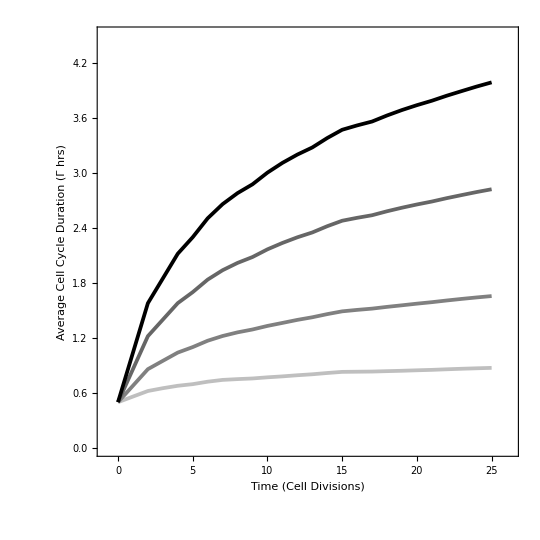

```mathematica
(*
markers = {{-Graphics-, 0.04}, {-Graphics-, 0.04}, {-Graphics-, 0.05}, {-Graphics-, 0.04}};
markers={-Graphics-,-Graphics-,-Graphics-}*)
gnF2=ListPlot[Transpose[{Range[0,25],#}]&/@diversity1,PlotRange->{{-0.85,26.25},{0,4.5}},FrameStyle->Directive[Opacity[1],Black],FrameTicksStyle->Opacity[1],AspectRatio->1,Axes->False,Frame->True,
(*PlotStyle->{Directive[{Lighter[Gray,0.5],Thickness[0.005]}],Directive[{ColorData["ThermometerColors"][0.15],Thickness[0.005]}],Directive[{Brown,Thickness[0.005]}],Directive[{Darker[Pink,0.1],Thickness[0.005]}]}*)PlotStyle->{Directive[{Lighter[Gray,0.5],Thickness[0.005]}],
Directive[{Lighter[Black,0.5],Thickness[0.005]}],
Directive[{Darker[Gray,0.2],Thickness[0.005]}],Directive[{Darker[Black,0.1],Thickness[0.005]}]},BaseStyle->{20},Joined->True,PlotMarkers->None(*{markers,5}*),FrameTicks->{Automatic,{Automatic,Automatic}},FrameLabel->{"Time (Cell Divisions)","Average Cell Cycle Duration (Γ hrs)"},(*PlotLabel->"Same Number of Genes",*)
(*Epilog->{(*Text[Style[dc[[1]]ToString[gNmeMax[[1]] ] ,28],Center,{1.3,-10.1}],Text[Style[dc[[2]]ToString[gNmeMax[[2]] ] ,28],Center,{-1.3,-5.1}],*)
Text[Style["Γ_1 1.00 hr",Lighter[Gray,0.5]],Center,{-3.4,12}],
Text[Style["Γ_2 hrs",ColorData["ThermometerColors"][0.15]],Center,{-0.4,-3}],Text[TableForm[{Style[#,Lighter[Gray,0.5]]&/@{1,2,5},Style[#,ColorData["ThermometerColors"][0.15]]&/@{1,2,5}},TableHeadings->{None,{"L_1","L_G","G"}}],Center,{-0.4,-5}]},*)
(*PlotLegends->(*Placed[*)LineLegend[Style[dc[[#]]ToString[gNmeMax[[#]] ] ,16]&/@Range[1,Length[dc]]](*,{Center,{-0.2,0.2}}*)(*,{Center,Right}]*),*)ImageSize->540,ImagePadding->{{Automatic, 10}, {Automatic, 10}},InterpolationOrder->1]
```

```mathematica
bc=Partition[{{4999,0,0,0,0,0},{9998,0,0,0,0,0},{14997,0,0,0,0,0},{19982,14,0,0,0,0},{24971,24,0,0,0,0},{29876,118,0,0,0,0},{34615,378,0,0,0,0},{38942,1048,2,0,0,0},{43880,1109,2,0,0,0},{48614,1374,2,0,0,0},{53261,1724,4,0,0,0},{57344,2632,12,0,0,0},{61422,3551,14,0,0,0},{64860,5080,46,0,0,0},{67474,7407,104,0,0,0},{69710,10014,258,2,0,0},{74417,10297,267,2,0,0},{78794,10892,294,2,0,0},{83111,11559,309,2,0,0},{86878,12752,348,2,0,0},{90820,13796,361,2,0,0},{94110,15456,410,2,0,0},{97150,17390,435,2,0,0},{99692,19748,532,4,0,0},{102613,21802,556,4,0,0},{105134,24138,696,6,0,0},{4999,0,0,0,0,0},{9998,0,0,0,0,0},{14239,758,0,0,0,0},{12928,6804,264,0,0,0},{8732,15721,542,0,0,0},{7264,18316,4330,84,0,0},{4298,20389,10026,280,0,0},{4166,18850,14402,2522,52,0},{1034,21203,20084,2618,52,0},{874,19690,24680,4656,90,0},{444,15643,32092,6699,111,0},{432,14870,32408,11476,802,0},{345,11096,36951,15687,908,0},{344,10788,35752,20558,2544,0},{306,9888,33137,27365,4289,0},{304,9842,32262,28600,8976,0},{33,5846,38530,31493,9081,0},{28,5310,38022,36510,10112,0},{14,3377,37520,43291,10779,0},{14,3284,36288,46114,14280,0},{10,2300,33362,53781,15526,0},{10,2274,32358,55212,20124,0},{10,1977,28886,60340,23764,0},{10,1970,28368,59864,29764,0},{6,1682,25052,64548,33687,0},{6,1664,24662,63966,39676,0},{4999,0,0,0,0,0},{9896,102,0,0,0,0},{68,9530,5392,7,0,0},{48,6372,5824,7240,512,0},{0,22,5529,18167,1277,0},{0,18,4430,15128,10418,0},{0,6,2195,8754,24038,0},{0,6,2194,8452,28708,632},{0,0,4,2066,42289,632},{0,0,4,1780,46918,1288},{0,0,4,998,51935,2052},{0,0,4,998,48902,10084},{0,0,2,630,53007,11348},{0,0,2,630,49634,19720},{0,0,2,608,42499,31876},{0,0,2,608,41776,37598},{0,0,0,0,46385,38598},{0,0,0,0,43104,46878},{0,0,0,0,36185,58796},{0,0,0,0,35314,64666},{0,0,0,0,28150,76829},{0,0,0,0,27340,82638},{0,0,0,0,22395,92582},{0,0,0,0,22108,97868},{0,0,0,0,17055,107920},{0,0,0,0,16956,113018},{4999,0,0,0,0,0},{4999,0,0,0,0,0},{2486,7512,0,0,0,0},{0,0,2598,12079,320,0},{0,0,1726,8074,10196,0},{0,0,0,5,24990,0},{0,0,0,4,20906,9084},{0,0,0,0,12212,22781},{0,0,0,0,11768,28224},{0,0,0,0,3152,41839},{0,0,0,0,2684,47306},{0,0,0,0,1698,53291},{0,0,0,0,1698,58290},{0,0,0,0,914,64073},{0,0,0,0,914,69072},{0,0,0,0,910,74075},{0,0,0,0,910,79074},{0,0,0,0,0,84983},{0,0,0,0,0,89982},{0,0,0,0,0,94981},{0,0,0,0,0,99980},{0,0,0,0,0,104979},{0,0,0,0,0,109978},{0,0,0,0,0,114977},{0,0,0,0,0,119706},{0,0,0,0,0,124705}},26];
```

```mathematica
legen=SwatchLegend[coloB,Reverse[{0,1,1.25,1.5,1.75,2,">2"}](*{"3.0","2.5","2.0","1.5","1.0","0.0"}*),LegendLayout->"Column",LegendMarkerSize->15,LegendLabel->Placed["Cell cycle duration, Γ hrs",Right,Rotate[Style[#,16],-90Degree]&]]
```

```mathematica
pie=Table[PieChart[#,ChartStyle->col[Union[Flatten[Select[(#/(#/. 0->1) *Range[1,6]),#>0&]&/@bc[[i]]]]](*ChartLabels->(If[If[incr1[[1]]==-3,#≠4,#≠3],"",Style[ToString[NumberForm[N[bc[[i,#]]]*100,{3,0}]]<>"%",14]]&/@pos[[i]])*)(*,Frame->True,FrameLabel->{None,"Frequency"},AspectRatio->1,Axes->False,Frame->True,BaseStyle->{16,Black},FrameStyle->Directive[{Black,Thickness[0.005]}],PlotRange->{{0.5,2.5},{0,1}},*)]&/@bc[[i]],{i,Length[bc]}];
```

{1,3,6,9,11,13,16,19,21,23,26}

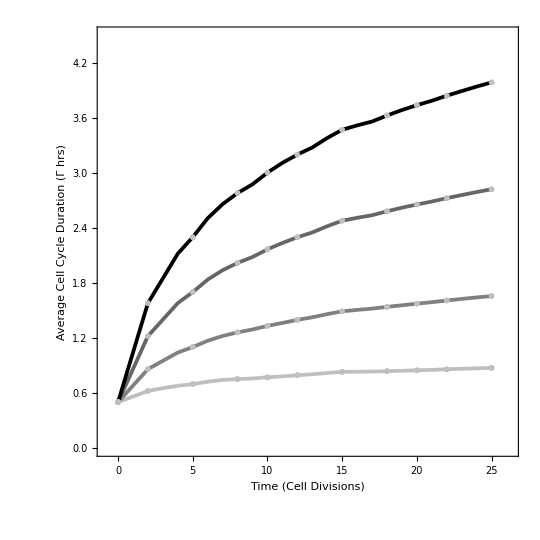

```mathematica
selDiv={1,3,6,9,11,13,16,19,21,23,26}
gnF4=Show[Show[gnF2,PlotStyle->Gray],Table[ListPlot[#[[1]],PlotRange->{{-0.85,26.25},{0,504.5}},FrameStyle->Directive[Opacity[1],Black],FrameTicksStyle->Opacity[1],AspectRatio->1,Axes->False,Frame->True,
PlotStyle->{Directive[{Lighter[Gray,0.5],Thickness[0.005]}],Directive[{ColorData["ThermometerColors"][0.15],Thickness[0.005]}],Directive[{Brown,Thickness[0.005]}],Directive[{Darker[Pink,0.1],Thickness[0.005]}]},BaseStyle->{20},Joined->True,PlotMarkers->Show[#[[2]],ImageSize->31],FrameTicks->{Automatic,{Automatic,Automatic}},FrameLabel->{"Time (Cell Divisions)","Transcriptome Diversity"},(*PlotLabel->"Same Number of Genes",*)
(*Epilog->{(*Text[Style[dc[[1]]ToString[gNmeMax[[1]] ] ,28],Center,{1.3,-10.1}],Text[Style[dc[[2]]ToString[gNmeMax[[2]] ] ,28],Center,{-1.3,-5.1}],*)
Text[Style["Γ_1 1.00 hr",Lighter[Gray,0.5]],Center,{-3.4,12}],
Text[Style["Γ_2 hrs",ColorData["ThermometerColors"][0.15]],Center,{-0.4,-3}],Text[TableForm[{Style[#,Lighter[Gray,0.5]]&/@{1,2,5},Style[#,ColorData["ThermometerColors"][0.15]]&/@{1,2,5}},TableHeadings->{None,{"L_1","L_G","G"}}],Center,{-0.4,-5}]},*)
(*PlotLegends->(*Placed[*)LineLegend[Style[dc[[#]]ToString[gNmeMax[[#]] ] ,16]&/@Range[1,Length[dc]]](*,{Center,{-0.2,0.2}}*)(*,{Center,Right}]*),*)ImageSize->540,ImagePadding->{{Automatic, 10}, {Automatic, 10}}]&/@Transpose[{Partition[Transpose[{selDiv-1,diversity1[[i,selDiv]]}],1],pie[[i,selDiv]]}],{i,1,4}]]
```

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/FigsourceFiles2019/output/6-Figure6_increasing.nb",gnF4(*GraphicsColumn[{gfAB,gfD},Spacings->-50]*)]
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/FigsourceFiles2019/output/6-Figure6_increasing.nb

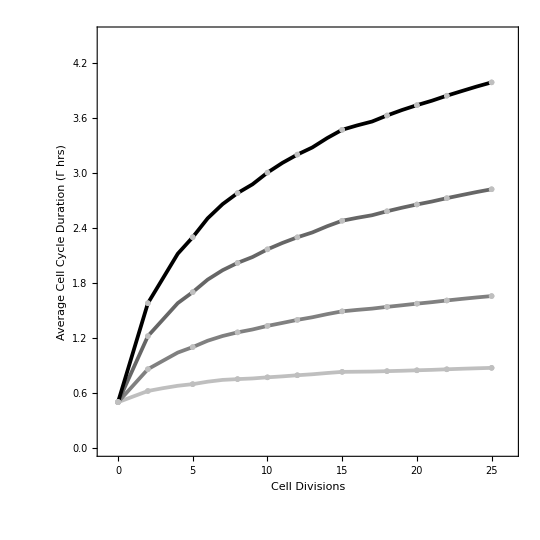
-Graphics-A

```mathematica
gfA=Panel[gnF4,Style["A",30,Black,Bold],Appearance->"Frameless",Background->White]
```

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/6-Figure6_increasing_A.nb",gfA(*GraphicsColumn[{gfAB,gfD},Spacings->-50]*)]
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/6-Figure6_increasing_A.nb